InterpolatingFunction::dmval: Input value {-5.34366} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0594671} lies outside the range of data in the interpolating function. Extrapolation will be used.

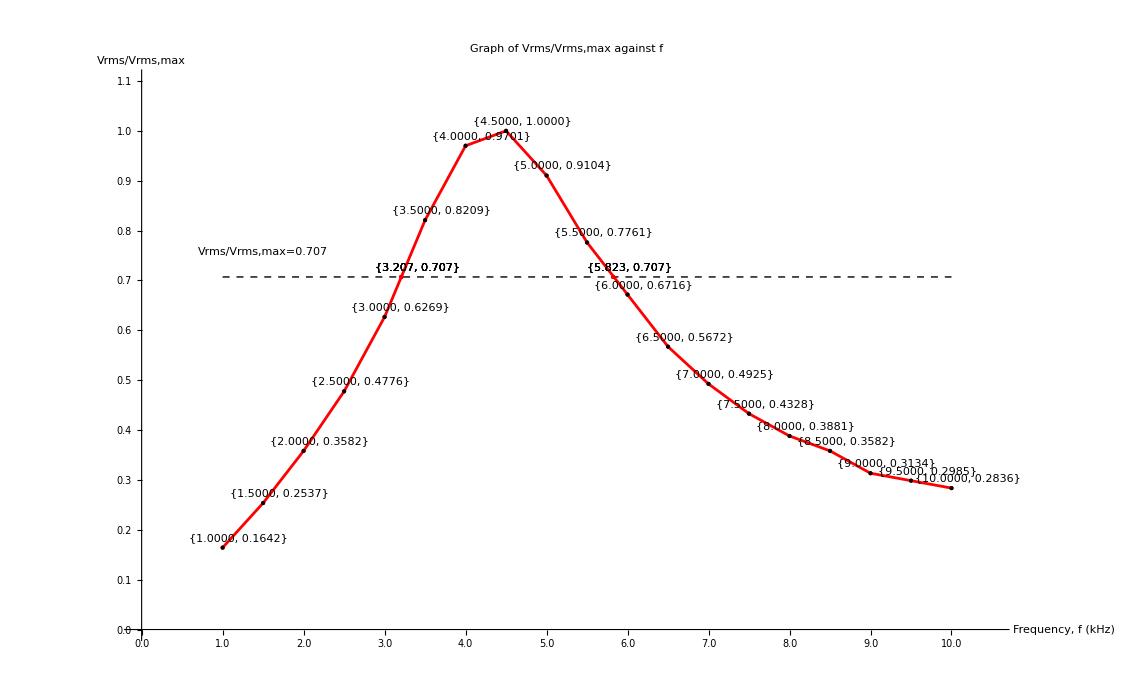

```mathematica
data={{1.0,0.1642},{1.5,0.2537},{2.0,0.3582},{2.5,0.4776},{3.0,0.6269},{3.5,0.8209},{4.0,0.9701},{4.5,1.0000},{5.0,0.9104},{5.5,0.7761},{6.0,0.6716},{6.5,0.5672},{7.0,0.4925},{7.5,0.4328},{8.0,0.3881},{8.5,0.3582},{9.0,0.3134},{9.5,0.2985},{10.0,0.2836}};

intersectionPoints={x,0.707}/. Table[FindRoot[Interpolation[data][x]==0.707,{x,xi}],{xi,1,10,1}];

ListLinePlot[data,PlotStyle->Red,Mesh->All,MeshStyle->PointSize[Medium],AxesLabel->{"Frequency, f (kHz)","Vrms/Vrms,max"},PlotLabel->"Graph of Vrms/Vrms,max against f",Epilog->{Dashed,Line[{{1,0.707},{10,0.707}}],Red,PointSize[Medium],Point[intersectionPoints],Text[Style[ToString@NumberForm[#,{4,3}],Black],#+{0.2,0.02}]&/@intersectionPoints,Black,PointSize[Medium],Point[data],Text[Style[ToString@NumberForm[#,{4,4}],Black],#+{0.2,0.02}]&/@data,Text["Vrms/Vrms,max=0.707",{1.5,0.707+0.05}]},PlotRange->{{0,10.5},{0,1.1}},
Ticks->{{#,NumberForm[#,{3,1}]}&/@Range[0,10.5,0.5],{#,NumberForm[#,{3,1}]}&/@Range[0,1.1,0.1]}
]
```